### DEVBIO 232 Homework 4 Samuel Morabito March 22, 2019

#### Problem1:

```mathematica
(* Define system based on the cartoon: *)
system1 = {mb'[t] == -f1*mb[t] + r1*cy[t],
		 cy'[t] == f1*mb[t] - r1 * cy[t] - f2*cy[t] + r2*nu[t],
		  nu'[t] == f2*cy[t] - r2*nu[t],
		   mb[0] == mbzero, cy[0] == cyzero, nu[0] == nuzero};

(* Define arbitrary parameters *)
params1 = {f1-> 2, r1-> 1, f2-> 1, r2 -> 1, mbzero-> 100, cyzero-> 0, nuzero-> 0};
```

```mathematica
k1 = (f1/r1)/.params1;
k2 = (f2/r2) /. params1;

(*Numerically solve the system*)
sol1 = NDSolve[system1 /. params1, {mb, cy, nu}, {t, 0, 150}];

(*compute steady state concentrations*)
mbss = (cy[50]/.sol1)/k1
cyss = cy[50]/.sol1
nuss= k2*cy[50]/.sol1
```

{20.}

{40.}

{40.}

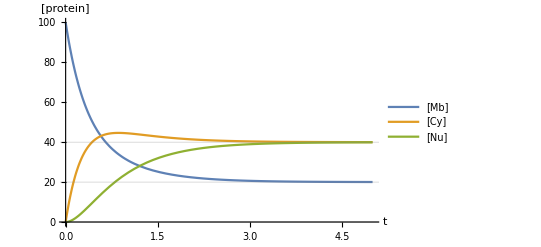

```mathematica
(* plot numerical solutions as a function of time *)
Plot[Evaluate[{mb[t], cy[t], nu[t]} /. sol1], {t,0,5}, PlotRange-> Full, GridLines-> {{20,0,40,0}},
PlotLegends-> {"[Mb]", "[Cy]", "[Nu]"}, AxesLabel-> {"t", "[protein]"}]
```

```mathematica
(* plot using Manipulate *)
Manipulate[
p = {f1-> f1val, f2-> f2val, r1-> r1val, r2-> r2val, mbzero-> mbzeroval, cyzero-> cyzeroval, nuzero-> nuzeroval};
s = NDSolve[system1 /. p, {mb, cy, nu}, {t,0,150}];
Plot[Evaluate[{mb[t], cy[t], nu[t]}/.s], {t,0,20}, PlotRange-> Full, PlotLegends-> {"[Mb]", "[Cy]", "[Nu]"}, AxesLabel-> {"t", "[protein]"}  ],
{{f1val,2}, 0, 10},
{{f2val,1}, 0, 10},
{{r1val,1}, 0, 10},
{{r2val,1}, 0, 10},
{{mbzeroval,100}, 50, 500},
{{cyzeroval,0}, 0, 500},
{{nuzeroval,0}, 0, 500}
]
```

#### Problem2:

```mathematica
system2 = {x'[t] == xmax* kd^n/(z[t]^n+kd^n)-dx*x[t],
                   z'[t]== zmax*x[t]-dz*z[t], x[0]==0.1, z[0]==0};
Manipulate[
p = {xmax-> xmaxval, zmax-> zmaxval, kd->kdval, n->nval, dx->1, dz->1};
s = NDSolve[system2 /. p, {x,z}, {t,0,100}];
Plot[{x[t] /. s, z[t] /.s}, {t,0,20}, PlotRange-> Full, PlotLegends-> {"x", "z"}, AxesLabel-> {"t", "[concentration]"}],
{{xmaxval, 10},0,50},
{{zmaxval, 1},0,50},
{{kdval, 10},0,50},
{{nval, 10},0,50}
]
```

#### Problem 3:

```mathematica
system3 = {
x'[t]==xmax * kz^nx/(z[t]^nx+kz^nx)-dx*x[t],
y'[t]==ymax * x[t]^ny/(x[t]^ny+kx^ny)-dy*y[t],
z'[t]==zmax * y[t]^nz/(y[t]^nz+ky^nz)-dz*z[t],
x[0] == 1, y[0]==0.1, z[0]==0.1
};
```

```mathematica
Manipulate[
p={xmax->1, ymax->1, zmax->1, dx->dxval, dy->dyval, dz->dzval, kx->kxval, ky->kyval, kz->kzval, nx->nxval, ny->nyval, nz->nzval};
s= NDSolve[system3 /.p, {x,y,z}, {t,0,100}];
Plot[{x[t] /. s, y[t] /.s, z[t] /.s}, {t,0,20}, PlotRange-> Full, PlotLegends-> {"x", "y",  "z"}, AxesLabel-> {"t", "[concentration]"}],
{{kxval, 0.5},0,5},
{{kyval, 0.5},0,5},
{{kzval, 0.5},0,5},
{{nxval, 8},0,50},
{{nyval, 4},0,20},
{{nzval, 4},0,20},
{{dxval, 1},0,10},
{{dyval, 1},0,10},
{{dzval, 1},0,10}
]
```